```mathematica
xc={{355.130529835391,1},{643.6426306782209,1000}};
yc={{143.89730482352007,10^-6},{371.0703248654638,10^-3}};
yfit=Quiet[Solve[{Exp[a+b*yc[[1,1]]]==yc[[1,2]],Exp[a+b*yc[[2,1]]]==yc[[2,2]]},{a,b}]];
yd[y_]:=Exp[yfit[[1,1,2]]+yfit[[1,2,2]] y]
xfit=Quiet[Solve[{Exp[a+b*xc[[1,1]]]==xc[[1,2]],Exp[a+b*xc[[2,1]]]==xc[[2,2]]},{a,b}]];
xd[x_]:=Exp[xfit[[1,1,2]]+xfit[[1,2,2]] x]
dat[list_]:=Table[{xd[list[[i,1]]],yd[list[[i,2]]]},{i,1,Length[list]}];
bl=dat[{{163.3930585232669,104.7425584639127},{191.44557217473886,120.7517163263692},{230.2429937282368,149.1665875276987},{259.6744791666667,165.1556144151631},{317.1584782565685,223.12778964862306},{355.58347677271286,252.99712379313084},{452.156796553498,304.58777995409946},{548.4331844531497,292.99737110240585},{642.4599358974359,246.68103038936377},{738.8571096470403,180.8930041152264}}];
ye=dat[{{162.65827793605575,295.45335005144034},{192.80441298670468,319.71117491690404},{232.18060007122506,355.8563405151947},{259.8002977603672,373.94905428933214},{318.54248278727454,416.2241017727129},{356.1421113287433,422.9629456513137},{451.2810991413422,412.97294931149094},{549.5202571027224,369.7769097222223},{644.1308068217791,315.3880480373536},{740.1253610715416,233.29896476337453}}];
gr=dat[{{162.12480709876542,239.44394487970877},{192.84467493668888,266.5150735003166},{230.82175925925924,297.7784776630263},{259.83552696660337,324.08966197768285},{318.9400695433682,367.2102104107313},{355.2613811728395,390.19475110794554},{452.78085677825266,395.61501612456476},{548.6747561530549,350.2347657486547},{643.4060917220639,290.70243995330804},{742.0126399770498,227.07849349081988}}];
db=dat[{{194.3041706236151,179.89652085311803},{230.7965955405192,212.0909826092117},{259.64931544792654,242.82091593463116},{319.09608459955683,288.41757429170616},{356.5950582660652,317.4061782803102},{453.23883645932256,352.52466415400437},{547.300817109845,321.5430936411839},{644.1861670030073,274.3460227722379},{740.1001973528015,198.2207408396644}}];
mid=dat[{{163.5692045544476,208.4321779044002},{192.00923947451724,233.651256825736},{234.03768251424503,267.58704791864517},{260.7867155349794,292.7356684275087},{318.5777119935106,344.4169139759418},{356.16224230373535,366.3244475110794},{452.4386302033871,378.62447323124405},{546.5610037788857,344.2961281259893},{643.9043333531181,285.7250563865147},{739.0785503719532,220.08297968106996}}];
```

```mathematica
sigs={0.02,0.05,.1,0.15,0.3};
```

```mathematica
transform[list_,sig_]:=Table[{list[[i,1]],list[[i,2]] list[[i,1]]/sig^2},{i,Length[list]}];
```

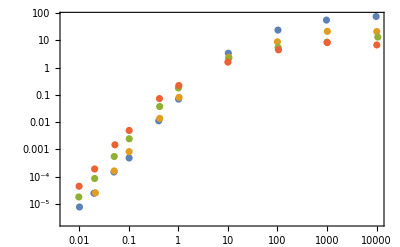

```mathematica
ListLogLogPlot[{transform[bl,sigs[[1]]],transform[db,sigs[[2]]],transform[gr,sigs[[3]]],transform[ye,sigs[[4]]]}]
```

```mathematica
Series[2σ^2 τ t+2 σ^2( Exp[-t/τ]-1),{t,0,2}]
```

(-(2 σ^2)/τ+2 σ^2 τ) t+(σ^2 t^2)/τ^2+O[t]^3

```mathematica
Solve[σ^2( τ-1/τ)==Dl,τ]
```

{{τ→(Dl-√(Dl^2+4 σ^4))/(2 σ^2)},{τ→(Dl+√(Dl^2+4 σ^4))/(2 σ^2)}}

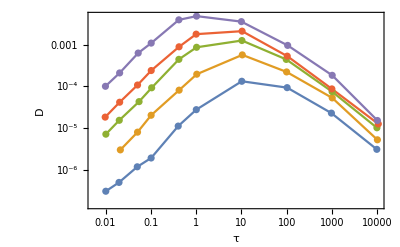

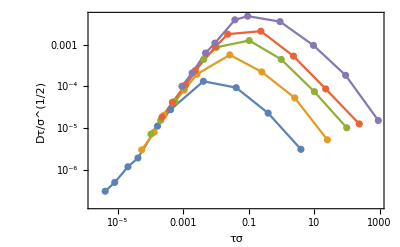

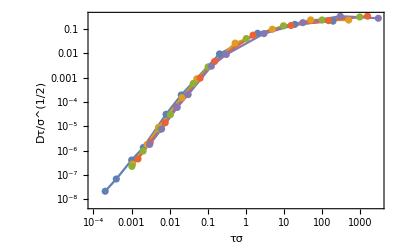

```mathematica
transform1[list_,sig_]:=Table[{list[[i,1]] sig^2,list[[i,2]]},{i,Length[list]}];
transform2[list_,sig_]:=Table[{list[[i,1]] sig^1,list[[i,1]]list[[i,2]]/sig^.5},{i,Length[list]}];
ListLogLogPlot[{bl,db,mid,gr,ye},Joined->True,Mesh->All,FrameLabel->{"τ","D"}]
ListLogLogPlot[{transform1[bl,sigs[[1]]],transform1[db,sigs[[2]]],transform1[mid,sigs[[3]]],transform1[gr,sigs[[4]]],transform1[ye,sigs[[5]]]},Joined->True,FrameLabel->{"τσ","Dτ/σ^(1/2)"},Mesh->All]
ListLogLogPlot[{transform2[bl,sigs[[1]]],transform2[db,sigs[[2]]],transform2[mid,sigs[[3]]],transform2[gr,sigs[[4]]],transform2[ye,sigs[[5]]]},Joined->True,FrameLabel->{"τσ","Dτ/σ^(1/2)"},Mesh->All]
```

```mathematica
xc={{181.89882010268556,.1},{756.9095885169827,10^4}};
yc={{157.49095946879933,10^-6},{157.1435624012638,10^-3}};
yfit=Quiet[Solve[{Exp[a+b*yc[[1,1]]]==yc[[1,2]],Exp[a+b*yc[[2,1]]]==yc[[2,2]]},{a,b}]];
yd[y_]:=Exp[yfit[[1,1,2]]+yfit[[1,2,2]] y]
xfit=Quiet[Solve[{Exp[a+b*xc[[1,1]]]==xc[[1,2]],Exp[a+b*xc[[2,1]]]==xc[[2,2]]},{a,b}]];
xd[x_]:=Exp[xfit[[1,1,2]]+xfit[[1,2,2]] x]
dat[list_]:=Table[{xd[list[[i,1]]],yd[list[[i,2]]]},{i,1,Length[list]}];
```

```mathematica
pg=dat[{{757.5529164198263,247.3980487263034},{641.6681168542652,310.10536384281204},{527.2844157286729,369.6475056773302},{412.0257886552132,412.34732301540294},{297.5691770339652,405.46371445497635},{184.13760120458136,341.98440585505534}}];
rg=dat[{{757.1411865620062,343.7428354561612},{641.3378751974724,394.9302922590837},{526.8898412815956,427.99305761255926},{412.5790506516587,437.7759305884676},{296.5956074743286,415.03643364928917},{181.56857844589257,348.8508590047394}}];
pb=dat[{{641.6252283274091,264.36046109794626},{527.6232350908372,312.84165185624016},{411.83279028436016,319.02617742891005},{296.76287272906785,268.7308019845972},{182.5292814474723,183.7900745458137}}];
rb=dat[{{757.0768537717217,298.3367520734598},{641.5608955371247,340.31175330766206},{526.4438006022906,345.4111991508689},{411.98718898104255,327.8869470774092},{294.98299886453395,270.79374012638243},{183.2369421406003,192.59508910939974}}];
resg=dat[{{641.5265847156397,332.6947509379939},{527.0485288309637,385.69210357424976},{412.77204902251185,421.06227167259095},{296.25249925947867,411.5195744470775},{181.7873099328594,345.9301503258296}}];
resb=dat[{{642.5773536236175,270.7079630726699},{526.7440202902844,304.79576421800954},{412.814937549368,311.3019537421012},{296.4283422195892,267.4613015896525},{182.13041814770926,193.76165703988949}}];
```

```mathematica
ss={0.02,.15};
```

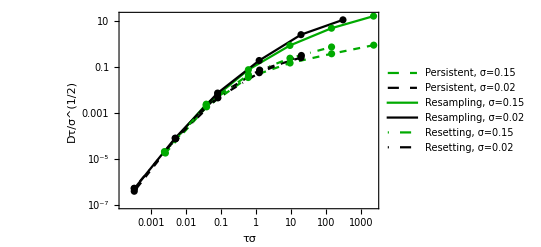

```mathematica
ListLogLogPlot[{transform2[pg,.15],transform2[pb,.02],transform2[rg,0.15],transform2[rb,.02],transform2[resg,0.15],transform2[resb,.02]},Joined->True,PlotStyle->{{Darker[Green],Dashed},{Black,Dashed},{Darker[Green]},{Black},{Darker[Green],DotDashed},{Black,DotDashed}},PlotLegends->{"Persistent, σ=0.15","Persistent, σ=0.02","Resampling, σ=0.15","Resampling, σ=0.02","Resetting, σ=0.15","Resetting, σ=0.02"},Joined->True,FrameLabel->{"τσ","Dτ/σ^(1/2)"},Mesh->All]
```

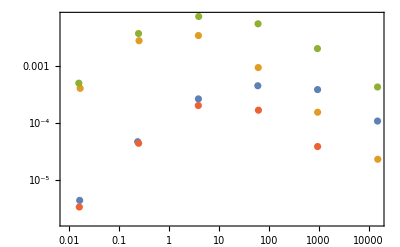

```mathematica
ListLogLogPlot[{rb,pg,rg,pb}]
```

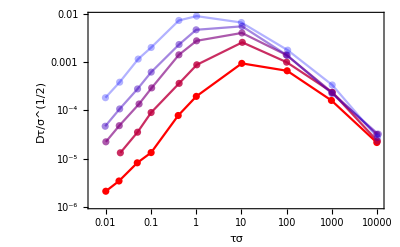

```mathematica
transform2[list_,sig_]:=Table[{list[[i,1]] sig^0,list[[i,2]]/sig^.5},{i,Length[list]}];
ListLogLogPlot[{transform2[bl,sigs[[1]]],transform2[db,sigs[[2]]],transform2[mid,sigs[[3]]],transform2[gr,sigs[[4]]],transform2[ye,sigs[[5]]]},Joined->True,FrameLabel->{"τσ","Dτ/σ^(1/2)"},Mesh->All,PlotStyle->redBluePlotConfig[5]]
```

```mathematica
{,}
```

```mathematica
xc={{63.55844606785176,10^-2},{323.1455960348313,10^4}};
yc={{56.39221399927828,3.9},{194.9476780206836,4.2}};
yd[yp_]:=Fit[yc,{1,y},y]/.y->yp
xfit=Quiet[Solve[{Exp[a+b*xc[[1,1]]]==xc[[1,2]],Exp[a+b*xc[[2,1]]]==xc[[2,2]]},{a,b}]];
xd[x_]:=Exp[xfit[[1,1,2]]+xfit[[1,2,2]] x]
dat[list_]:=Table[{xd[list[[i,1]]],yd[list[[i,2]]]},{i,1,Length[list]}];
q5=dat[{{62.636517133150406,61.21333206244594},{75.94033183777121,66.43363584991721},{93.31203916148665,79.53310548138262},{106.164393820764,94.76869395897302},{132.09245705648868,134.37837267410583},{149.24081046303417,159.63637415832073},{192.8946207422436,196.1452351935947},{236.00192675603722,204.80613974768343},{279.77929452134066,206.5193118144867},{323.09094560828976,207.2772894695633}}];
q4=dat[{{62.80997283478236,56.530028118383115},{75.9973583698146,58.56159832242864},{93.10531798282936,62.37287154732803},{106.04796465117543,68.88577672778271},{132.30393044614954,90.97405347258626},{149.64712450384326,108.93503496074996},{192.93501453577431,137.58136289054255},{235.75956399485284,145.71239591772817},{279.6105910307123,146.52977621034995},{322.7250253610113,146.49175852232105}}];
q3=dat[{{322.64186166844814,122.83049993532087},{279.6058388197087,121.67333655594058},{236.04707276057155,121.06742965297964},{192.62136860953575,113.92485651454597},{149.57346523328727,88.20351445747858},{132.9739921976593,74.57417329911013},{106.53744238454779,60.50762872840909},{93.15521619836734,57.43532431457183},{76.01874331933087,55.80056372932822},{62.58186670660882,55.349103683984765}}];
q2=dat[{{323.05055181475905,93.21947317179445},{279.9575024339762,93.55212794204752},{235.79520557738,91.9244956733093},{192.57384649949955,85.59455061649382},{149.40476174265893,67.85692304550003},{131.89286419433682,62.39900870784794},{106.38774773793394,57.074156278297096},{92.87008353815044,56.29954588470781},{76.18982291546102,55.69601508724867},{62.39177826646423,55.7031434037541}}];
q1=dat[{{322.6822554619788,72.33588191640743},{278.23957815616933,72.65665615915145},{236.27755499424688,70.36846656091069},{193.39360289762317,66.22453856575825},{149.65187671484688,57.71332865828339},{132.22314285908806,55.795811518324655},{106.43526984797008,55.11624534480765},{93.06492418929865,55.950258375942155},{75.5910443290055,54.55786055188284},{62.59374723411787,55.242178936403434}}];
qset={q1,q2,q3,q4,q5};
```